```mathematica
Raketenwurf[thetap_,yp_,mWp_]:=Module[{y,mW,x,t,dt,vx,vy,Aaustritt,p0,pa,V0,rhoW,k,ausgabeliste,rhola,mleer,g,Aquer,cw,V,rholi,p,m,va,mWa,fp,fpx,fpy,fd,fdx,fdy,theta,v},
theta=thetap;
y=yp;
mW=mWp;
x=0;
t=0;
dt=0.0001;
vx=0;
vy=0;
Aaustritt=(0.0128)^2*Pi;
p0=300000;
pa=100000;
V0=0.0015;
rhoW=997;
k=1;
ausgabeliste={{x,y}};
rhola=1.25;
mleer=0.13057;
cw=0.6482;
g=10 cw*-9.81;
Aquer=((0.09/2)^2)*Pi;

V=V0-(mW/rhoW);
rholi=(rhola*p)/pa;
(*Antriebsphase/Wasser*)
While[mW>0,
	(*Antrieb*)
		m=mleer+mW+(rholi*V);
		p=(p0*V0)/V;
		va=k*(Sqrt[(2*(p-pa))/rhoW]);
		mWa=(Aaustritt*va*dt*rhoW);
		mW=mW-mWa;
		
		fp=(mWa*va)/dt;
		fpx=fp*Cos[theta];
		fpy=fp*Sin[theta];
		
		V=V0-(mW/rhoW);
		rholi=(rhola*p)/pa;
	(*Ort*)
		x=vx*dt+x;
		y=vy*dt+y;
	
	(*Luftwiderstand*)
			v=Sqrt[vy^2+vx^2];
			fd=1/2* Aquer*rhola*cw*v^2;
			fdx=-fd*Cos[theta];
			fdy=-fd*Sin[theta];
	(*Geschwindigkeit*)
			vx=((fpx+fdx)/m)*dt+vx;
			vy=((fpy+fdy)/m+g)*dt+vy;
			theta=ArcTan[vy/vx];
	t=t+dt;
	AppendTo[ausgabeliste,{x,y}];
		
];
(*Antriebsphase/Luft*)

(*Gleitphase*)
	While[y≥0,
	(*Ort*)
			x=vx*dt+x;
			y=vy*dt+y;
			
	(*Luftwiderstand*)
			v=Sqrt[vy^2+vx^2];
			fd=1/2* Aquer*rhola*cw*v^2;
			fdx=-fd*Cos[theta];
			fdy=-fd*Sin[theta];
			

	(*Geschwindigkeit*)
			vx=(fdx/m)*dt+vx;
			vy=((fdy/m)+g)*dt+vy;
			theta=ArcTan[vy/vx];
	
	t=t+dt;
AppendTo[ausgabeliste,{x,y}]
	];
Print["Flugzeit: ",t,"s"];
Print["Flugweite: ",x,"m"];
ListPlot[ausgabeliste]

]
```

Flugzeit: 3.0161s

Flugweite: 44.2023m

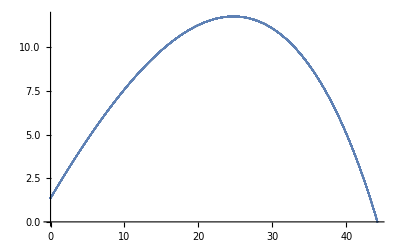

```mathematica
Raketenwurf[40°,1.36,0.4]
```

Flugzeit: 2.6922s

Flugweite: 43.1843m

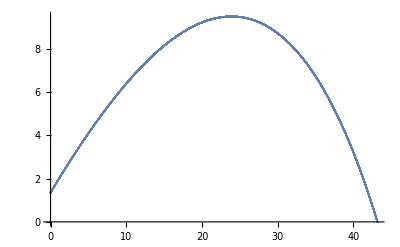

```mathematica
Raketenwurf[35°,1.35,0.4]
```

Flugzeit: 4.6979s

Flugweite: 47.3175m

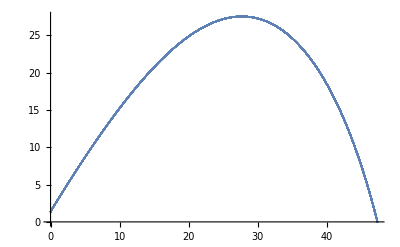

```mathematica
Raketenwurf[60°,1.38,0.6]
```

Flugzeit: 4.5197s

Flugweite: 79.37m

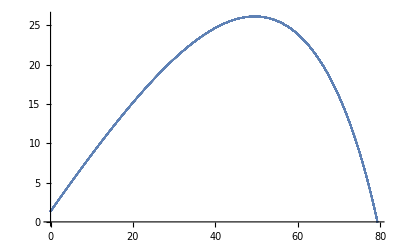

```mathematica
Raketenwurf[40°,1.33,1.2]
```

Flugzeit: 3.2358s

Flugweite: 55.5032m

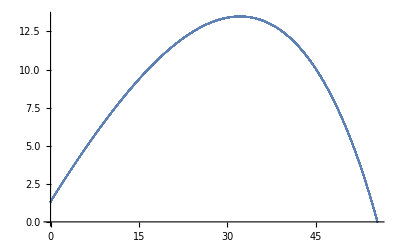

```mathematica
Raketenwurf[37°,1.33,0.6]
```

Flugzeit: 3.7475s

Flugweite: 55.7779m

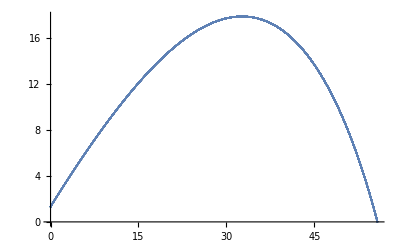

```mathematica
Raketenwurf[40°,1.33,0.6]
```

Flugzeit: 3.2318s

Flugweite: 50.6191m

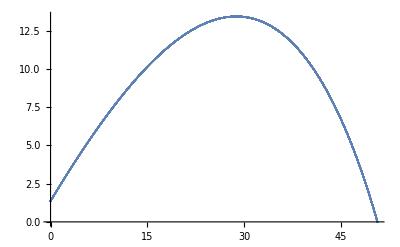

```mathematica
Raketenwurf[40°,1.36,0.5]
```

Flugzeit: 3.4413s

Flugweite: 56.2672m

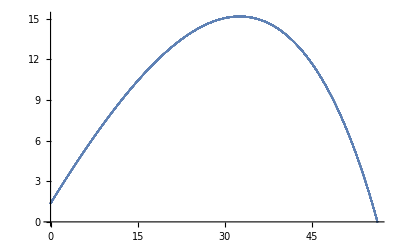

```mathematica
Raketenwurf[40°,1.36,0.6]
```

Flugzeit: 0.3667s

Flugweite: 14.8352m

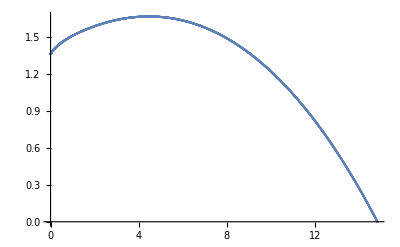

```mathematica
Raketenwurf[40°,1.36,1]
```